## Definitions Section

### Game definitions

```mathematica
(*This commented out version of ma  handles the case where pa= and pb=0. In that case the normal ma is undefined. It doesn't matter, because the condition never happens (they never collaborate) But the division by zero makes mathematica balk.  Uncomment this version if you want to redo the jacobian calculations. *)
(*ma[pa_, pb_, wa_] :=If[pa==1&&pb==0, 0, (wa(1-pa(1-pb)))/(wa(1-pa(1-pb)) + (1-wa)(pa*pb + 0.5(1-pa)pb))]; *)
ma[pa_, pb_, wa_, coin_] := (wa(1-pa(1-pb)))/(wa(1-pa(1-pb)) + (1-wa)(pa*pb + coin(1-pa)pb)); 
fa[pa_, pb_, wa_, coin_] := wa(1-pa(1-pb)) + (1-wa)(pa*pb + (1-pa)pb coin);
fb[pa_,pb_, wa_, coin_] := (1-wa)((1-pa)(1-pb) + (1-pa)pb(1-coin));
nobias[epsilon_ , chi_] := (1-epsilon)(1-chi)/(1-epsilon*chi);
firstbias[epsilon_ , chi_] := epsilon(1-chi)/(1-epsilon*chi);
mattbias[epsilon_ , chi_] := (1-epsilon)chi/(1-epsilon*chi);
pia[pa_,pb_, wa_, coin_,ba_, bb_, epsilon_, chi_, chat_] := 

(* They collaborate and Adams is first, paper is worth 1 + chat*)
fa[pa, pb, wa,coin](nobias[epsilon, chi]*(ma[pa, pb, wa, coin]*ba +(1-ma[pa, pb, wa,coin])(1-bb)) + firstbias[epsilon, chi])(1+chat) +
(*They collaborate and Babbage is first, papyer is worth 1 + chat *)
 fb[pa,pb, wa, coin]nobias[epsilon,chi](1-bb)(1+chat)  + 
(* They don't collaborate papers are collectively worth 1*)
pa(1-pb)(wa*ba + (1-wa)(1-bb));
pib[pa_, pb_, wa_,coin_, ba_, bb_, epsilon_,chi_, chat_] := 
(*They collaborate and Adams is first, paper is worth 1 + chat *)fa[pa,pb,wa,coin](nobias[epsilon,chi]*(ma[pa, pb, wa,coin](1-ba) + (1-ma[pa, pb, wa,coin])bb )+mattbias[epsilon,chi])(1+chat) +
(* They collaborate and Babbage is first, paper is worth 1 + chat *)
fb[pa, pb, wa,coin]*(nobias[epsilon,chi]*bb + firstbias[epsilon,chi] + mattbias[epsilon, chi])(1+chat) + 
(* They don't collaborate, papers are collectively worth 1 *)
pa(1-pb)(wa(1-ba) + (1-wa)bb);
```

### Dynamics definitions

```mathematica
RepA[pa_, pb_, wa_, coin_,ba_, bb_,epsilon_,chi_, chat_]:=pa*(pia[1, pb, wa,coin,ba, bb,epsilon,chi,chat] - pia[pa, pb, wa, coin,ba, bb,epsilon,chi,chat]);
RepB[pa_, pb_, wa_, coin_,ba_, bb_,epsilon_, chi_, chat_]:=pb*(pib[pa, 1, wa,coin,ba, bb,epsilon,chi, chat] - pib[pa, pb, wa, coin,ba, bb,epsilon,chi,chat]);
```

### Simulations definitions

```mathematica
RepSolve[pastart_, pbstart_, wa_, coin_,ba_, bb_, epsilon_, chi_, chat_, time_]:= 
NDSolve[{x'[t] == RepA[x[t], y[t], wa, coin, ba, bb, epsilon,chi, chat], y'[t] ==RepB[x[t],y[t],wa, coin,ba, bb, epsilon,chi, chat], x[0] == pastart, y[0] == pbstart}, {x, y}, {t, 0, time}]
SimRep[nsim_, wa_, coin_,ba_, bb_, epsilon_,chi_, chat_, time_] :=Module[{StartingPt, arg,s}, Table[StartingPt = RandomPoint[Cuboid[{0,0}, {1,1}]
, 1];
arg = Join[StartingPt[[1]], {wa,coin, ba, bb, epsilon, chi, chat, time}];
s = Apply[RepSolve, arg];
Evaluate[{x[time], y[time]} /.s][[1]], 
nsim
]];
CountAlph[nsim_] := Count[Map[EuclideanDistance[{1,1}, #] &, nsim], p_/;p<0.01];
CountWork[nsim_] := Count[Map[EuclideanDistance[{0,0}, #] &, nsim], p_/;p<0.01];
```

### Some housekeeping functions

```mathematica
(*The expectation calculations for beta distributions with non-whole number parameters is slow. This allows for caching*)
ClearAll[BaCalc, BbCalc];
BaCalc[alpha_, beta_]:=BaCalc[alpha, beta]=Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
BbCalc[alpha_, beta_]:=BbCalc[alpha, beta]=1-Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
```

## Analyzing the game

### Looking at Replicator dynamics

```mathematica
Manipulate[StreamPlot[{RepA[pa,pb, wa,coin,ba, bb,epsilon, chi, chat], RepB[pa,pb, wa,coin,ba, bb, epsilon,chi,chat]}, {pa,0,1}, {pb,0,1}, Frame -> False, Axes->True, AxesOrigin->{0,0},AxesLabel->{"pa", "pb"}], {wa, 0.0001, 1}, {ba, 1/2, 1}, {bb, 1/2, 1}, {epsilon,0,1}, {chi, 0, 1-epsilon},{chat,0,2}, {coin, 0, 1}]
```

## Beta distribution examples

### Basins of attraction

#### alpha + beta = 100, chat = 1, epsilon = 0.1, chi = 0, coin = 0 .1 to 0.9

```mathematica
gaps = 10;
coinlist = {0.1, 0.3, 0.5, 0.7, 0.9};
total = 100;
sims = 1000;
epsilon=0.1;
nalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa,coin, localba, localbb, epsilon,0,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{coin,coinlist}] ;
nwork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa,coin, localba, localbb, epsilon,0,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{coin, coinlist}] ;
```

```mathematica
nalpha
```

{{231/250,417/500,361/500,333/500,559/1000,101/200,381/1000,147/500,3/20},{437/500,191/250,659/1000,111/200,127/250,431/1000,169/500,229/1000,137/1000},{199/250,343/500,597/1000,253/500,9/20,399/1000,321/1000,211/1000,63/500},{71/100,581/1000,247/500,441/1000,387/1000,8/25,263/1000,47/250,1/10},{163/250,543/1000,217/500,347/1000,153/500,63/200,11/50,161/1000,43/500}}

```mathematica
nwork
```

{{23/250,83/500,129/500,349/1000,41/100,251/500,72/125,89/125,33/40},{113/1000,121/500,169/500,411/1000,483/1000,281/500,617/1000,19/25,177/200},{169/1000,61/200,393/1000,47/100,563/1000,601/1000,693/1000,759/1000,891/1000},{7/25,393/1000,62/125,597/1000,589/1000,657/1000,183/250,203/250,111/125},{17/50,527/1000,583/1000,129/200,659/1000,703/1000,771/1000,829/1000,449/500}}

```mathematica
gaps = 10;
coinlist = {0.1, 0.3, 0.5, 0.7, 0.9};
nalpha = {{231/250,417/500,361/500,333/500,559/1000,101/200,381/1000,147/500,3/20},{437/500,191/250,659/1000,111/200,127/250,431/1000,169/500,229/1000,137/1000},{199/250,343/500,597/1000,253/500,9/20,399/1000,321/1000,211/1000,63/500},{71/100,581/1000,247/500,441/1000,387/1000,8/25,263/1000,47/250,1/10},{163/250,543/1000,217/500,347/1000,153/500,63/200,11/50,161/1000,43/500}};
nwork = {{23/250,83/500,129/500,349/1000,41/100,251/500,72/125,89/125,33/40},{113/1000,121/500,169/500,411/1000,483/1000,281/500,617/1000,19/25,177/200},{169/1000,61/200,393/1000,47/100,563/1000,601/1000,693/1000,759/1000,891/1000},{7/25,393/1000,62/125,597/1000,589/1000,657/1000,183/250,203/250,111/125},{17/50,527/1000,583/1000,129/200,659/1000,703/1000,771/1000,829/1000,449/500}};
```

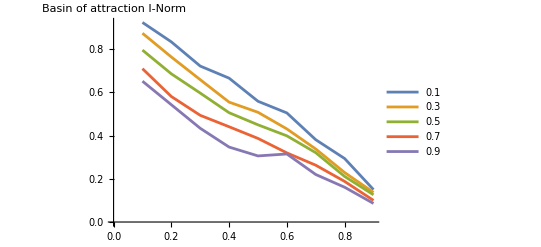

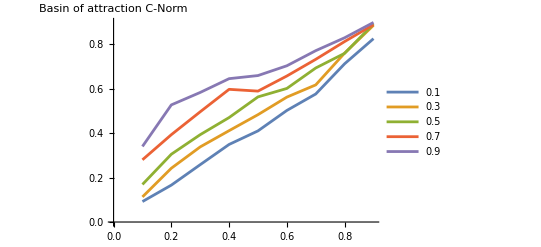

```mathematica
ListLinePlot[nalpha, PlotLegends-> Map[( "" <> ToString[#])&, coinlist], DataRange ->{1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[nwork, PlotLegends-> Map[( "" <> ToString[#])&,coinlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```